```mathematica
(*
Code supplement to:"Dynamical Analysis of Attractor Behavior in Constant Roll Inflation",[arXiv:1904.06289].

Copyright (C) 2019  Michael M.J.Morse

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General 
Public License as published by the Free Software Foundation, either version 3 of the License, or (at your option) 
any later version.This program is distributed in the hope that it will be useful,but WITHOUT ANY WARRANTY;
without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.

See the GNU General Public License for more details. 
You should have received a copy of the GNU General Public License along with this program.If not,see<https://www.gnu.org/licenses/>.
*)
```

```mathematica
ClearAll/@Names["Global`*"];
Remove/@Names["Global`*"];

(* Set up η and t0/tf values to generate plots *)
nlist = {3.0115,2,2.5,3.5};
t0list = {0.4,0.4,0.3,0.2};
tendlist = {100,8,8,8};
```

-Graphics-

-Graphics-

-Graphics-

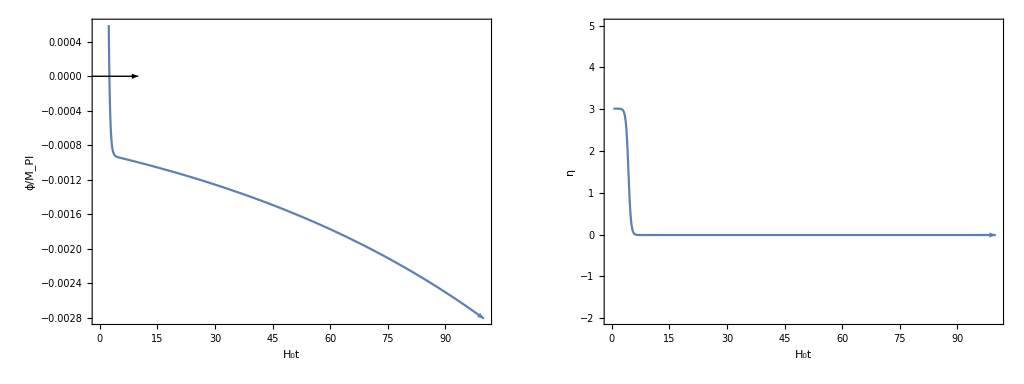

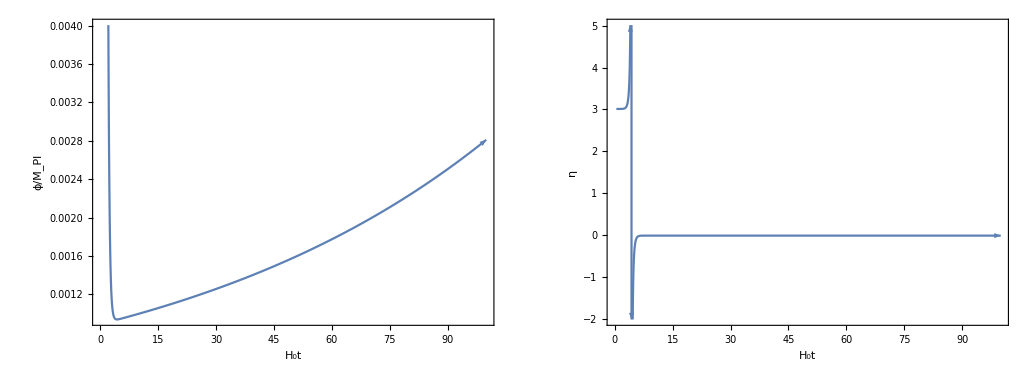

-Graphics-

-Graphics-

-Graphics-

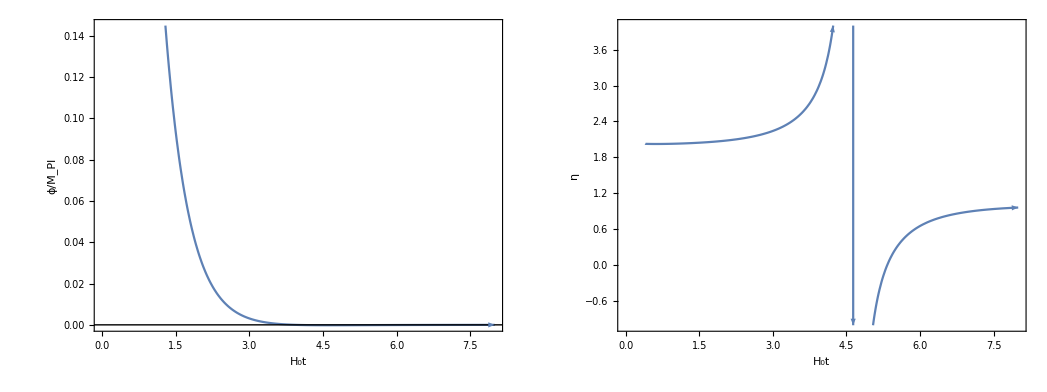

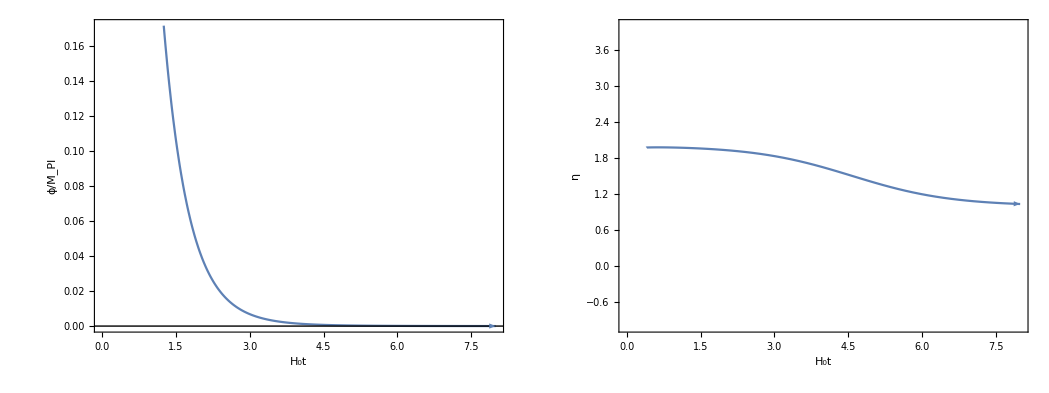

-Graphics-

-Graphics-

-Graphics-

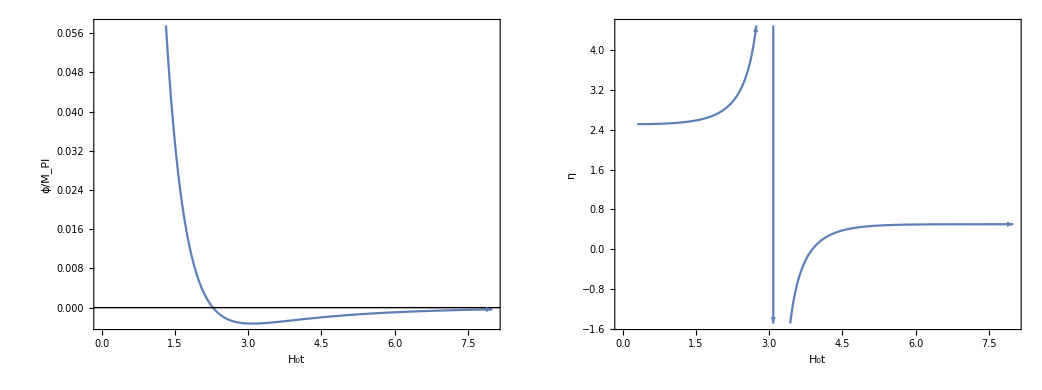

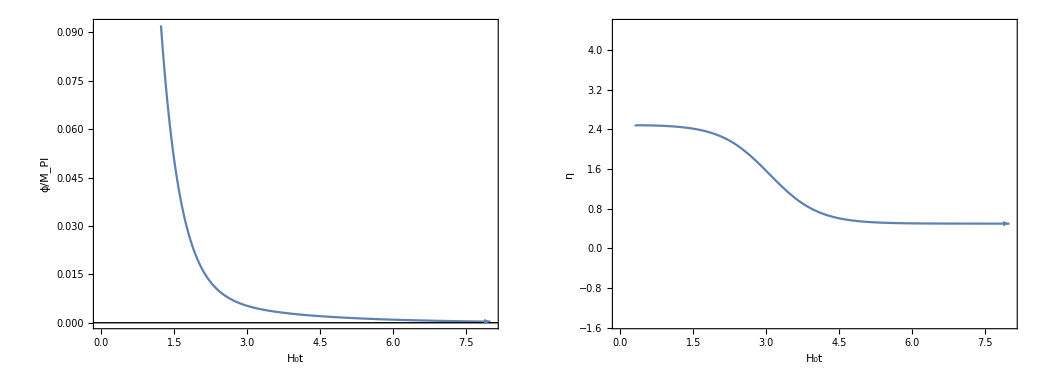

-Graphics-

-Graphics-

-Graphics-

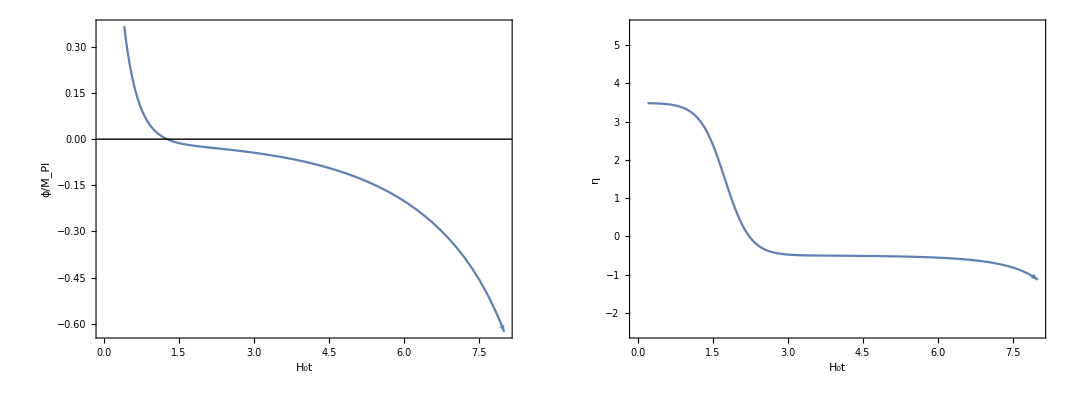

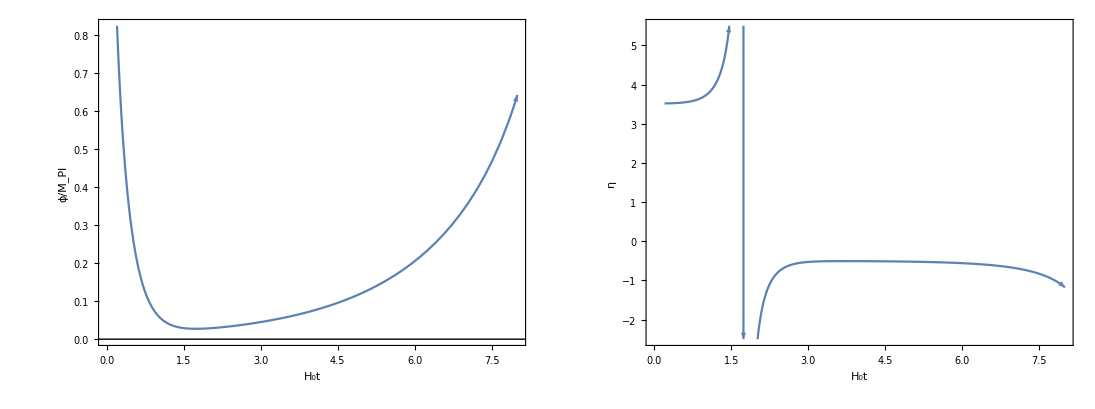

```mathematica
For[i=1,i<Length[nlist]+1,i++,
(****** Clears all used parameters ******)
Remove[s,s2,s3,sn2,sn3,η,V];
Clear[s,s2,s3,sn2,sn3,η,V];

 (***** Define the /eta value for the constant roll solution *****)
n =nlist[[i]];
H0=(1);
tend=tendlist[[i]]; 
t0 =t0list[[i]]; (* for 2.5 t0 = 0.3 for 3.5 t0 = .2 for 2 us t0=.4 *)
agoal =50; (* Accuracy Goal *) 
pgoal=50;(* Precision Goal *)
wgoal = 50;(* Working Precision *)
method = Automatic; (* As the system is differential-algebraic methods are limited *)

(****** Define analytical solutions ******)
analyticϕ[t_]:=Sqrt[2/n]Log[Coth[n/2 t]]; 
analyticH[t_]:= H0  Coth[n  t] ;
analyticη[t_]:= - H0 analyticϕ''[ t]/(analyticH[t] analyticϕ'[t]);
analyticϵ[t_]:= - analyticH'[ t]/analyticH[t]^2;
HH = Sqrt[(H0^2(ϕ'[t])^2/2 + V)/3];
η:= - H0 ϕ''[t]/( HH *ϕ'[t]);
ϵ= - H0 H'[t]/H[t]^2; (*Definition of epsilion here ' denotes d/dt*)


(****** Exact Potential ******)
V=3  (1+1/3 (3-n) Sinh[(√n ϕ[t])/(√2)]^2) ;

(****** System of equations the numerical solver will use ******)
eqs ={H0^2 ϕ''[t] + 3 H0 (Sqrt[(H0^2(ϕ'[t])^2/2 + V)/3]) ϕ'[t]  + D[V,ϕ[t]]==0 ,H[t]==(Sqrt[(H0^2(ϕ'[t])^2/2 + V)/3]) } ; 

(****** define the perturbation in ϕ' ******)
δ=analyticϕ'[t0]/100; 
If[n == 3.0115,δ=analyticϕ'[t0]/1000 ];




(****** Numerically evolve the exact solution for consistancy check ******)
s=NDSolve[{eqs,ϕ[t0]==analyticϕ[t0],ϕ'[t0]==analyticϕ'[t0]},{ϕ,H},{t,t0,tend},AccuracyGoal->agoal,PrecisionGoal->pgoal,WorkingPrecision->wgoal,
Method->method];

(***** Numerically evolve the Perturbations, we will evolve 2 pertubation in each direction ******)
s2=NDSolve[{eqs,ϕ[t0]==analyticϕ[t0],ϕ'[t0]==analyticϕ'[t0]+δ},{ϕ,H},{t,t0,tend},AccuracyGoal->agoal,PrecisionGoal->pgoal,WorkingPrecision->wgoal,
Method->method];

s3=NDSolve[{eqs,ϕ[t0]==analyticϕ[t0],ϕ'[t0]==analyticϕ'[t0]+2δ},{ϕ,H},{t,t0,tend},AccuracyGoal->agoal,PrecisionGoal->pgoal,WorkingPrecision->wgoal,
Method->method];


s2n=NDSolve[{eqs,ϕ[t0]==analyticϕ[t0],ϕ'[t0]==analyticϕ'[t0]-δ},{ϕ,H},{t,t0,tend},AccuracyGoal->agoal,PrecisionGoal->pgoal,WorkingPrecision->wgoal,
Method->method];

s3n=NDSolve[{eqs,ϕ[t0]==analyticϕ[t0],ϕ'[t0]==analyticϕ'[t0]-2δ},{ϕ,H},{t,t0,tend},AccuracyGoal->agoal,PrecisionGoal->pgoal,WorkingPrecision->wgoal,
Method->method];


(***** Generates Plots ******)
legend = {"Analytic","Unperturbed","δ","2δ","-δ","-2δ"};
arrow = Arrowheads[{0,.03,.03,0}];
style = {{Dashing[Tiny],arrow,Interpreter["Color"]["RGB 0 0 0"]},
{Dashing[Large],arrow,Interpreter["Color"]["RGB 197 27 138"],Thick},
{DotDashed,arrow,Interpreter["Color"]["RGB 116 206 227"],Thick},
{DotDashed,arrow,Interpreter["Color"]["RGB 31 120 180"],Thick},
{arrow,Interpreter["Color"]["RGB 178 223 138"],Thick},
{arrow,Interpreter["Color"]["RGB 51 160 44"],Thick}};
ftstyle = Directive[Black,Bold,14] ;
spticks = {{0,None},{None,None}};

ϕplot=Plot[{Evaluate[analyticϕ[t]],Evaluate[{ϕ[t]}/.s],Evaluate[{ϕ[t]}/.s2],Evaluate[{ϕ[t]}/.s3],
Evaluate[{ϕ[t]}/.s2n],Evaluate[{ϕ[t]}/.s3n]
},{t,tend,t0},
FrameLabel->{Style["H_0t",FontSize->20,Black],Style["ϕ/M_Pl",FontSize-> 20,Black]},PlotRange->Full,
PlotLegends->Placed[legend,{1,.8}],
PlotStyle->style,Frame-> True,FrameTicksStyle->ftstyle]/.Line->Arrow;


ηplot = Plot[{Evaluate[analyticη[t]],Evaluate[{η}/.s],Evaluate[{η}/.s2],Evaluate[{η}/.s3],Evaluate[{η}/.s2n],Evaluate[{η}/.s3n]},{t,tend,t0},
FrameLabel->{Style["H_0t",FontSize->20,Black],Style["η",FontSize->20,Black]},PlotRange->{(3-n) - 2,n + 2},
PlotLegends->Placed[legend,{1,0.8}],
PlotStyle->style,Frame->True,FrameTicksStyle->ftstyle]/.Line->Arrow;

ϵplot = LogLogPlot[{Evaluate[analyticϵ[t]],Evaluate[{ϵ}/.s],Evaluate[{ϵ}/.s2],Evaluate[{ϵ}/.s3],Evaluate[{ϵ}/.s2n],Evaluate[{ϵ}/.s3n]},{t,tend,t0},
FrameLabel->{Style["H_0t",FontSize->20,Black],Style["ϵ",FontSize->20,Black]},PlotRange->Automatic,
PlotLegends->Placed[legend,{1,0.8}],
PlotStyle->style,Frame->True,FrameTicksStyle->ftstyle]/.Line->Arrow;

p1 = Plot[{Evaluate[{ϕ[t]}/.s3]
},{t,tend,t0},
FrameLabel->{Style["H_0t",FontSize->13,Black],Style["ϕ/M_Pl",13,Black]},PlotRange->Automatic,
PlotStyle->{arrow},Frame-> True,FrameTicks->spticks,
Epilog->Line[{{-10,0},{10,0}}]]/.Line->Arrow;

p2 = Plot[{Evaluate[{η}/.s3]
},{t,tend,t0},
FrameLabel->{Style["H_0t",FontSize->13,Black],Style["η",FontSize-> 13,Black]},PlotRange->{(3-n) - 2,n + 2},
PlotStyle->{arrow},Frame-> True,FrameTicks->spticks]/.Line->Arrow;

overshootplot = Graphics[{Inset[p1,{0.25,0.25},Automatic,0.45],Inset[p2,{0.75,0.25},Automatic,0.45]},Ticks->None];

p3 = Plot[{Evaluate[{ϕ[t]}/.s3n]
},{t,tend,t0},
FrameLabel->{Style["H_0t",FontSize->13,Black],Style["ϕ/M_Pl",FontSize-> 13,Black]},PlotRange->Automatic,
PlotStyle->{arrow},Frame-> True,FrameTicks->spticks,
Epilog->Line[{{-10,0},{10,0}}]]/.Line->Arrow;

p4 = Plot[{Evaluate[{η}/.s3n]
},{t,tend,t0},
FrameLabel->{Style["H_0t",FontSize->13,Black],Style["η",FontSize-> 13,Black]},PlotRange->{(3-n) - 2,n + 2},
PlotStyle->{arrow},Frame-> True,FrameTicks->spticks]/.Line->Arrow;

undershootplot = 
Graphics[{Inset[p3,{0.25,0.25},Automatic,0.45],Inset[p4,{0.75,0.25},Automatic,0.45]},Ticks->None];


Print[ϕplot];
Print[ηplot];
Print[ϵplot];
Print[overshootplot];
Print[undershootplot];

]
```